# Chamber leak test

## Result

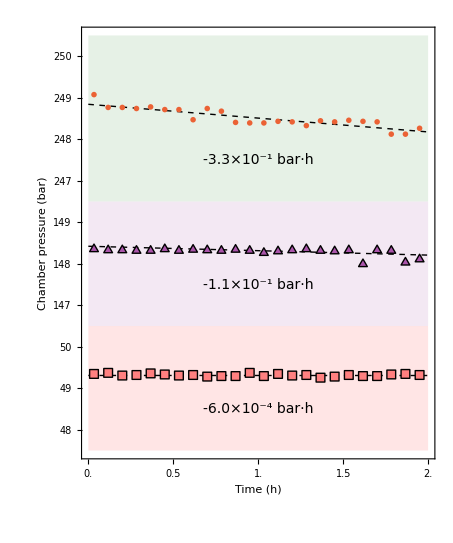

```mathematica
(* -- import data -- *)
dt=Import[NotebookDirectory[]<>"data/pressure.mx"];

(* -- data correction for cutouts -- *)
{δ1,δ2}={193,96};
dt[[1,All,2]]-=δ1;
dt[[2,All,2]]-=δ2;

(* -- fit -- *)
Clear[a,b,t];
lm=LinearModelFit[#,t,t]&/@dt;
fdt=Table[{t,lm[[i]][t]},{i,3},{t,0,2,.1}];
leak=#["BestFitParameters"][[2]]&/@lm;

(* -- axes cutout -- *)
cut=Graphics[{
{White,Polygon[{{-3,-3},{-3,-1},{3,3},{3,1}}]},
{Black,AbsoluteThickness[1],Line[{{-3,-1},{3,3}}]},
{Black,AbsoluteThickness[1],Line[{{-3,-3},{3,1}}]}
}];

(* -- plot -- *)
gf=ListLinePlot[

Flatten[{fdt,dt[[All,120;;;;300]]},1],


Prolog->{
{Lighter@Pink,Opacity[.3],Rectangle[{0,47.5},{2,50.5}]},
{Nest[Lighter,Purple,3],Opacity[.3],Rectangle[{0,50.5},{2,53.5}]},
{Lighter@RGBColor[.53,.73,.53],Opacity[.3],Rectangle[{0,53.5},{2,57.5}]}
},

Epilog->{
(* axes cutout *)
Inset[cut,{0,50.5},{0,0},{.3,.3}],
Inset[cut,{2,50.5},{0,0},{.3,.3}],
Inset[cut,{0,53.5},{0,0},{.3,.3}],
Inset[cut,{2,53.5},{0,0},{.3,.3}],
(* leak *)
Text[Style[StringForm["`1` bar·`2`",ScientificForm@SetPrecision[leak[[1]],2],Superscript["h","-1"]],{FontColor->Black,FontSize->14,FontWeight->Plain}],{1,54.5},{0,0}],
Text[Style[StringForm["`1` bar·`2`",ScientificForm@SetPrecision[leak[[2]],2],Superscript["h","-1"]],{FontColor->Black,FontSize->14,FontWeight->Plain}],{1,51.5},{0,0}],
Text[Style[StringForm["`1` bar·`2`",ScientificForm@SetPrecision[leak[[3]],2],Superscript["h","-1"]],{FontColor->Black,FontSize->14,FontWeight->Plain}],{1,48.5},{0,0}]
},

PlotRange->{{0,2},{47.5,250.5-δ1}},
Joined->{True,True,True,False,False,False},

PlotStyle->Flatten[{
ConstantArray[Directive[Black,AbsoluteThickness[1],AbsoluteDashing[4]],3],
ConstantArray[Directive[{}],3]
},1],

PlotMarkers->{
None,None,None,
Graphics[{EdgeForm[{Black,AbsoluteThickness[1]}],FaceForm[{RGBColor[.53,.73,.53,1]}],Disk[{0,0},Offset[4]]}],
{Graphics[{
EdgeForm[{Black,Opacity[1],AbsoluteThickness[1]}],
FaceForm[{Lighter@Purple,Opacity[1]}],
RegularPolygon[3]},PlotRangePadding->0],Offset[9]},
{Graphics[{
EdgeForm[{Black,Opacity[1],AbsoluteThickness[1]}],
FaceForm[{Pink,Opacity[1]}],
RegularPolygon[4]},PlotRangePadding->0],Offset[9]}
},

Axes->False,
Frame->True,
FrameLabel->{{"Chamber pressure (bar)",None},{"Time (h)",None}},
FrameTicks->{
{Table[{i,Which[i<50.5,i,i<53.5,i+δ2,i<57.5,i+δ1],{.015,0}},{i,48,63}],
Table[{i,Null,{.015,0}},{i,48,63}]},
{Table[{i/6,If[Mod[i,3]==0,N@(i/6),Null],{If[Mod[i,3]==0,.015,.008],0}},{i,0,12}],
Table[{i/6,Null,{If[Mod[i,3]==0,.015,.008],0}},{i,0,12}]}
},
FrameStyle->Directive[Black,AbsoluteThickness[1]],

LabelStyle->{FontColor->Black,FontFamily->"Arial",FontSize->14,FontWeight->Plain},

GridLines->None,

PlotRangeClipping->False,
ImagePadding->{{50,10},{45,10}},
ImageSize->(80*2)*(72/25.4),
AspectRatio->1.2

];

Print[gf];

Export[NotebookDirectory[]<>"leak.pdf",gf];
```